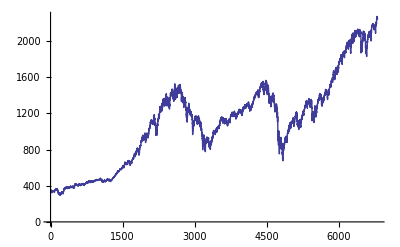

```mathematica
(* Analyzing the behavior of financial data *)

closingValues=FinancialData["SP500","Close","Jan 1., 1990","Value"];
ListLinePlot[closingValues]
```

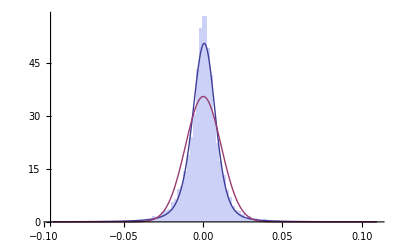

```mathematica
logr=Differences[Log[closingValues]];
edist1=EstimatedDistribution[logr,StableDistribution[1,α,β,μ,σ]];
edist2=EstimatedDistribution[logr,StableDistribution[1,2,0,μ1,σ1]]; (* Gauss *)
Show[Histogram[logr,Automatic,"PDF"],Plot[{PDF[edist1,x],PDF[edist2,x]},{x,Min[logr],Max[logr]},PlotRange->All,PlotStyle->Thick]]
```

```mathematica
edist1
```

StableDistribution[1,1.57582,-0.137138,0.000108547,0.00566342]

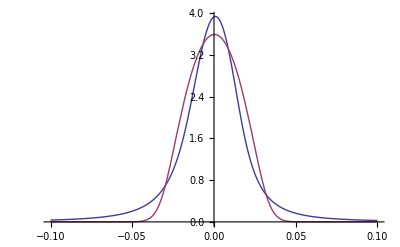

```mathematica
f1[x_]:=Log[1+PDF[edist1,x]];
f2[x_]:=Log[1+PDF[edist2,x]];

Plot[{f1[x],f2[x]},{x,-0.1,+0.1},PlotStyle->Thick]
```

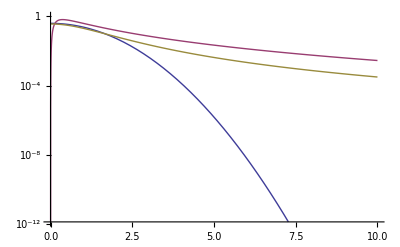

```mathematica
LogPlot[{PDF[NormalDistribution[0,1],x],PDF[LogNormalDistribution[0,1],x],PDF[StudentTDistribution[0,1,3],x]},{x,0,+10},PlotStyle->Thick]
```